# The package VQM`FastFourier`

Bernd Thaller
Institute of Mathematics
University of Graz
Austria
04-10-2004

### Abstract

Mathematica has a very efficient algorithm for calculating the Fourier transformation of a list. We use it for an approximate calculation of the Fourier transformation of a function.

This package VQM`FastFourier` provides commands for the numerical Fourier transform of complex-valued functions that are given as a list of complex values on a suitable grid of space points. This package is part of the VQM packages which can be obtained here:  http://www.uni-graz.at/imawww/vqm/software.html (free download). The VQM packages are part of the Visual Quantum Mechanics project, see http://www.uni-graz.at/imawww/vqm/. In particular, these packages are distributed with the book Advanced Visual Quantum Mechanics, Springer-Verlag New York, 2004.

This notebook describes the application of Mathematica's fast Fourier algorithm to the Fourier transform of a complex-valued function. The package VQM`FastFourier` implements this method. The

## Fourier transform of a list

The discrete Fourier transform of a list of n complex numbers {a_1, a_2, ... , a_n} is again a list of n complex numbers which is defined by

(1)        (a^⋀)_s = 1/(√n)∑_(r=1)^n a_r Exp[-ⅈ(2π)/n(s-1)(r-1)],    s = 1, ... , n .

In Mathematica, this operation is implemented by the command InverseFourier:

{(a^⋀)_1,... , (a^⋀)_n} = InverseFourier[{a_1,... , a_n}]

As the name suggests this function is inverse to Fourier[], which is defined by a reversed sign in the exponent. (The name is only a matter of convention. For the purpose of quantum mechanics, the definition with a minus in the exponent is more common).

The formula (1) has a certain symmetry. If we multiply the whole equation (1) by the s-dependent phase factor Exp[2π ⅈ(m(s-1))/n], this is the same as a cyclic permutation of the coefficients a_r:

(a^⋀)_s Exp[2π ⅈ(m(s-1))/n]= 1/(√n)∑_(r=1)^n a_r Exp[-2π ⅈ((r-1-m)(s-1))/n]= 1/(√n)∑_(r=1)^n b_r Exp[-ⅈ(2π)/n(s-1)(r-1)]

where b_r= a_((r+m)(mod n)), or

{b_1,... ,b_n} = RotateLeft[{a_1,... ,a_n},m].

## Fourier transform of a function

For an integrable function ψ(x), the Fourier transform is given by

(2)        ψ^⋀(k) = 1/(√(2π))∫_(-∞)^∞ ψ(x)  e^(-ⅈ k x)ⅆx.

We may approximate this integral by a finite Riemann sum. To this purpose we assume that the function ψ is reasonably well localized within a finite interval [x_0, x_n]. We divide this interval into n subintervals by introducing equally spaced points x_r,

x_0 < x_1< x_2< ... < x_n

and define

dx = x_r - x_(r-1) .

The Riemann sum approximating the Fourier integral is then given by

(3)        ψ^⋀(k) ≈ 1/(√(2π)) ∑_(r=1)^n ψ(x_r)e^(-ⅈ k x_r)dx

## Applying the command InverseFourier

This sum (3) looks already similar to (1). We set

k_s = (2π)/(n dx)(s-1)  and  x_r = x_1 + (r-1)dx

and obtain

(4)        ψ^⋀(k_s) ≈ 1/(√(2π)) ∑_(r=1)^n ψ(x_r)e^(-ⅈ k_s x_1)Exp[-ⅈ(2π)/n(s-1)(r-1)] dx

We see that the built-in discrete Fourier transform is obviously suitable to calculate (a numerical approximation of) the Fourier integral ψ^⋀(k)at the points k_s which are given by

{k_1, k_2, k_3, ... , k_n} = {0, (2π)/(n dx), (4π)/(n dx), ... , (2(n-1)π)/(n dx)} ,

These points form a grid in k-space where the distance between neighbouring points is

dk = (2π)/(n dx)= (2π)/(x_n-x_0)

and the length of the interval in Fourier space is  n dk = 2π/dx. It depends on the distance dx between the grid points in x-space.

Eq. (4) can be described as the (inverse) Fourier transform of a list, except that the result is multiplied by an s-dependent phase factor e^(ⅈ k_s x_1).

1/(√(2π)) ∑_(r=1)^n ψ(x_r)e^(-ⅈ k_s x_1)Exp[-ⅈ(2π)/n(s-1)(r-1)]dx
            = √(n/(2 π)) dx 1/(√n) ∑_(r=1)^n ψ(x_r)e^(-ⅈ k_s x_1)Exp[-ⅈ(2π)/n(s-1)(r-1)]dx

The element with index s in the list InverseFourier[{ψ(x_1), ... ,ψ(x_n)}] has to be multiplied by the phase factor  e^(ⅈ k_s x_1). This multiplication by an s-dependent phase factor can be achieved more effectively by a cyclic permutation of the elements {ψ(x_1), ... ,ψ(x_n)}. We define

ind[x] := (x-x_0)/dx

This is the index number of the point x in the sequence {x_1,x_2, ... ,x_n}. Hence ind[x_1]=1, and ind[0] = -x_0/dx. In Mathematica, the cyclic permutation is performed by the command RotateLeft:

{a_1, ... ,a_n} = RotateLeft[{ψ(x_1), ... ,ψ(x_n)},ind[0]]

This has precisely the same effect as the multiplication with the phase factor in (4). Hence the Fourier transform of the function is given by

(4')        ψ^⋀(k_s) ≈ √(n/(2 π)) dx 1/(√n)  ∑_(r=1)^n a_r Exp[-ⅈ(2π)/n(s-1)(r-1)]
                             =  √(n/(2 π)) dx  InverseFourier[{a_1, ... ,a_n}].

Discrete Fourier sums can be treated as periodic functions. In particular, if p = 2π/dx is the length of the interval in k-space, we can use Eq. (3) and find, using e^(ⅈ (α ± 2π)) = e^(ⅈ α)

ψ^⋀(k_s±p)= dx/(√(2π)) ∑_(r=1)^n a_r e^(-ⅈ (k_s ± p)dx (r-1)) = dx/(√(2π)) ∑_(r=1)^n a_r e^(-ⅈ k_s dx (r-1))= ψ^⋀(k_s).

Usually, we are interested in an interval in momentum space, which is symmetric with respect to the origin. Using the periodicity in k-space, we can correct this again by a RotateLeft command. Since  ψ^⋀(k_s) is periodic, we obtain the values of ψ^⋀ at the n points:

{-π/dx+ dk, ... , -dk, 0, dk, 2dk, ... , π/dx}

(which are obtained from {k_1, k_2, k_3, ... , k_n} by shifting these points n/2 + 1 places towards the left) by performing the cyclic permutation

RotateLeft[{ ψ^⋀(k_1), ψ^⋀(k_2), ... ,  ψ^⋀(k_n)}, n/2+1] .

## Practical implementation

Assume that we are given a function f[x] which vanishes outside an interval [a, b]. We want to determine a discrete approximation for the Fourier transform, suitable for plotting it quickly.
We first choose a grid of points on the x-axis. We assume that the grid points are equally spaced by dx and given by the numbers n dx. Since it is best to choose n as a power of 2, we calculate dx:

```mathematica
dx=(b-a)/n
```

```mathematica
xgrid=Table[Floor[a/dx] dx+k dx,{k,1,n}]
```

Of course, the size of dx depends on the variation of the given function. dx determines the size of the interval in k-space, where the values of the Fourier transform are calculated. The spacing of the points in k-space depends on the size of the interval [a,b]. If we want to evaluate the k-values at points which are closer together, we have to choose the interval in x-space larger. The points in xgrid are inside the significant interval [a,b]. We determine the function values at these points:

```mathematica
fvals=f/@xgrid
```

Next we rotate the list of function values

```mathematica
ind[x_]:=Floor[(x-a)/dx]+1
```

```mathematica
RotateLeft[fvals,ind[0]-1]
```

From this, we calculate the discrete Fourier transform

```mathematica
√(n/(2 π)) dx InverseFourier[RotateLeft[fvals,ind[0]-1]]
```

The result has been multiplied by the appropriate factor. Finally, the result is rotated by n/2

```mathematica
RotateLeft[√(n/(2 π)) dx InverseFourier[RotateLeft[fvals,ind[0]-1]],Round[n/2+1]]
```

## Explicit example

This is the function we want to transform:

```mathematica
f[x_]=(1/π)^(1/4) Exp[-x^2/2+I 2 x];
```

We choose an interval and grid points in x-space:

```mathematica
n=512;
a=-10;b=14;
```

```mathematica
dx=(b-a)/n;
```

```mathematica
xgrid=Table[Floor[a/dx] dx+k dx,{k,1,n}];
```

Note that 0 is an element of xgrid. Now we evaluate the function on the grid points. This gives the discretization of the function f:

```mathematica
fvals=f/@xgrid;
```

The following definition is useful for identifying the value of f at a particular point:

```mathematica
ind[x_]:=Floor[(x-a)/dx]+1
```

Next, we compute the Fourier transform of this list, as described above:

```mathematica
kvals=Chop[RotateLeft[√(n/(2 π)) dx InverseFourier[RotateLeft[fvals,ind[0]-1]],Round[n/2]]];
```

This list may be interpreted as a discretization of the Fourier transform of the function f. The grid in k-space is given by:

```mathematica
kleft=-π/dx;kright=π/dx;dk=(2 π)/(n dx);
```

In order to visualize the result, we load the package

```mathematica
<<"VQM`ArgColorPlot`"
```

This is the original function (or rather its discretization)

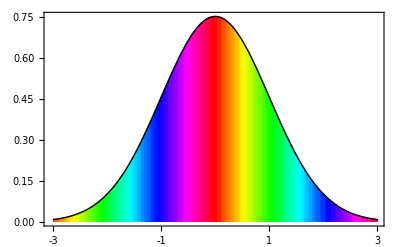

```mathematica
QListArgColorPlot[Take[fvals,{ind[-3],ind[3]}],Frame->True,FrameTicks->{QNiceTicks[-3,3,dx],Automatic}]
```

The following function is needed in order to extract parts of the Fourier-transformed list:

```mathematica
indk[k_]:=Floor[(k-kleft)/dk]+1;
```

Now we can plot the interesting part of the list kvals

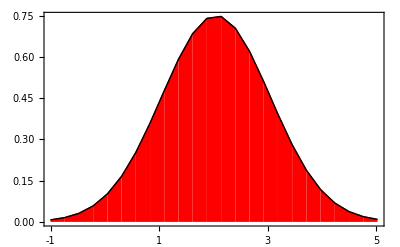

```mathematica
QListArgColorPlot[Take[kvals,{indk[-1],indk[5]}],Frame->True,FrameTicks->{QNiceTicks[-1,5,dk],Automatic},PlotRange->All]
```

We can easily combine the computation above in a single function. The following computes the Fourier transform of a numerically given function xlist and returns the list of Fourier-transformed values together with the information about the grid in k-space:

```mathematica
fourierList[xlist_,{xleft_,xright_}]:=Module[{n,dx,a,b,klist,kleft,kright,dk},n=Length[xlist]-1;dx=(xright-xleft)/n;a=-xleft/dx;b=xright/dx;klist=√(n/(2 π)) dx RotateLeft[InverseFourier[RotateLeft[xlist,Round[a]]],Round[n/2+1]];kleft=-π/dx;kright=π/dx;{klist,{kleft,kright}}];
```

This function is implemented as QFourierList in the package VQM`FastFourier`

## The package VQM`FastFourier`

The results described above form the theoretical background of the package VQM`FastFourier`. Here we show how to obtain the Fourier transform of a function f with the help of this package. The package VQM`ArgColorPlot` will be useful for the visualization of the function and its Fourier transform.

This loads all declarations of the VQM packages:

```mathematica
Needs["VQM`"]
```

The most important function defined by VQM`FastFourier` is QFourierList. (Note that all symbols defined by the VQM packages start with the letter Q.)

The first argument of QFourierList is a list flist of complex numbers. You may interpret this list as the discretization of a function defined in some interval [a,b]. The second argument of QFourierList specifies this interval. Hence the function is called like this: QFourierList[flist,{a,b}]. In order to have an example, we generate a list of complex values from a function f. The package VQM`FastFourier` provides some auxiliary functions for this.

We repeat the example above with the help of this package and consider the function

```mathematica
f[x_]=(1/π)^(1/4) Exp[-x^2/2+I 2 x];
```

in the interval [-10,14]:

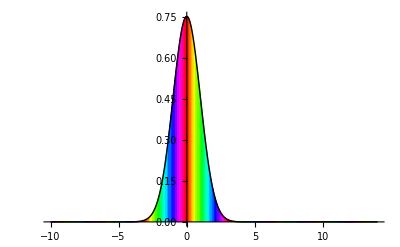

```mathematica
QArgColorPlot[f[x],{x,-10,14},PlotRange->All]
```

Let us first generate a suitable grid in x-space:

```mathematica
a = -10.; b = 14.; n = 512;
```

```mathematica
xgrid = QGrid[a,b,n];
```

This command divides the interval [-10,10] by equally spaced points x_0 =a< x_1< x_2< ... < x_n= b and returns the list { x_1, x_2, ... , x_n}. The number n should be even. You can obtain information about the space grid via the following functions.

```mathematica
{QLeftBorder[a,b,n],QRightBorder[a,b,n],QSpaceStep[a,b,n]}
```

{-9.98438,13.9688,0.046875}

QIndexPosition[x,a,b,n] lets you access the element of xgrid corresponding to a special value of x

```mathematica
QIndexPosition[5.,a,b,n]
```

321

```mathematica
xgrid[[321]]
```

5.01563

We can now define a discretization of the function f by

```mathematica
fvals = f /@ QGrid[a,b,n];
```

Usually, the function in position space will be the result of a numerical computation, and the list fvals of complex numbers is the object to start with.

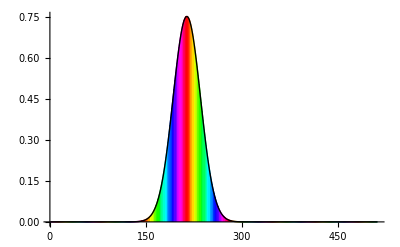

```mathematica
QListArgColorPlot[fvals,PlotRange->All]
```

The option QHorizontalRange lets you specify the plot range on the horizontal axis:

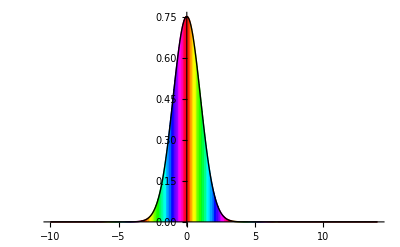

```mathematica
QListArgColorPlot[fvals,PlotRange->All, QHorizontalRange->QSpaceInterval[a,b,n]]
```

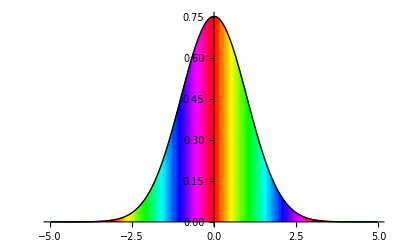

```mathematica
QListArgColorPlot[fvals,PlotRange->All, QHorizontalRange->{QSpaceInterval[a,b,n],{-5,5}}]
```

The points in x-space determine the interval and the grid in k-space, as explained above. You can obtain a list of the points in k-space by QFourierGrid[-10.,10,100]. Information about the grid in Fourier space can be obtained by

```mathematica
{kleft,kright,dk}={QFourierLeftBorder[a,b,n],QFourierRightBorder[a,b,n],QFourierStep[a,b,n]}
```

{-66.7588,67.0206,0.261799}

Hence

```mathematica
QFourierGrid[a,b,n]==Table[n,{n,kleft,kright,dk}]
```

True

If the function in x-space is given on the points of QGrid, then QFourierList returns the values of the Fourier transform on the points QFourierGrid in k-space.

```mathematica
Ff = QFourierList[fvals,{a,b}];
```

QFourierList returns the list of Fourier values and the interval in k-space: {Fflist,{kleft,kright}}.

```mathematica
Ffvals = Ff[[1]]; kinterval = Ff[[2]];
```

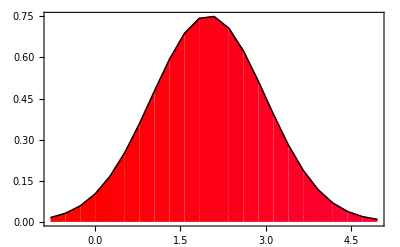

```mathematica
QListArgColorPlot[Ffvals,PlotRange->All, QHorizontalRange->{kinterval,{-1,5}},Frame->True]
```

This is the discretization of a shifted Gaussian function.

We can (approximately) reverse the whole process by QInverseFourierList.

```mathematica
result = QInverseFourierList[Ff];
```

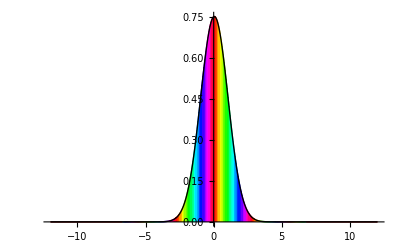

```mathematica
QListArgColorPlot[result[[1]],PlotRange->All,QHorizontalRange->result[[2]]]
```

Now the interval in x-space is symmetric with respect to x = 0.

Computing the Fourier transformation again gives the same result as before (up to numerical errors)

```mathematica
{testFfvals, testkinterval} = QFourierList[result];
```

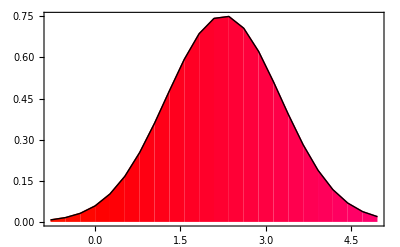

```mathematica
QListArgColorPlot[testFfvals,PlotRange->All,QHorizontalRange->{testkinterval,{-1,5}},Frame->True]
```

The numerical error is:

```mathematica
Max[Abs[testFfvals-Ffvals]]
```

0.133285